```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
lT=20;
V1=Flatten[Transpose[Table[Flatten[Import["./dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
```

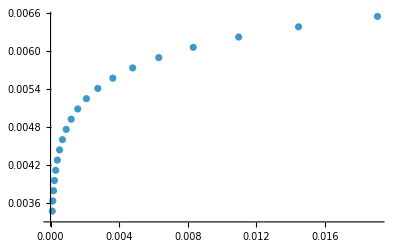

```mathematica
ListPlot[Transpose[{T,V1}],ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
V1
```

{0.0034652845009380943901532776517288382,0.0036268502092455416680641215530797769,0.0037885201204016666130740601904736561,0.0039502935849001043986085092316288834,0.0041121699806494983250322687399625922,0.0042741487108163595717672406592081347,0.0044362292019103990126221796697721236,0.004598410902077533171104057061944338,0.0047606932795717405463590636627108984,0.0049230758213817656696432614099496326,0.0050855580319925379540666587163773137,0.0052481394322643270631483443227893348,0.0054108195584152375376285526057924742,0.0055735979610947712273084003506402776,0.0057364742059047776024545672777743647,0.0058994479557905100320382805432814677,0.0060625186184755831108626382795547569,0.0062256858891756765827549231827848224,0.0063889493793382543066450006658960205,0.0065523087106995160987054980735151124}